```mathematica
αcont=SetPrecision[{0.5137193759431391,0.0024666827878353577},100]; 
σcont=SetPrecision[{0.16955497884544793,0.0008581023195660334},100];
ccont=SetPrecision[{-0.15956635071361625,0.0024752900407607015},100];
```

```mathematica
Πpar[θ_,v_,mD_]:=SetPrecision[mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]),100];
Πper[θ_,β_,v_,mD_]:=SetPrecision[mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]),100];
```

```mathematica
N[(z MeijerG[{{-1},{}},{{-1,0},{1/2}},z x^2]-Conjugate[z]MeijerG[{{-1},{}},{{-1,0},{1/2}},Conjugate[z] x^2])/(-ⅈ Im[z])/.{x->3,z->1+ⅈ}]
```

0.00997891+0. ⅈ

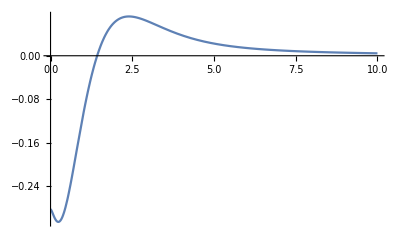

```mathematica
Plot[x^2 MeijerG[{{-1},{}},{{-1,0},{1/2}},x^2],{x,0,10},PlotRange->All]
```

```mathematica
Integrate[x^2 MeijerG[{{-1},{}},{{-1,0},{1/2}},a x^2],x]
```

1/2 x^3 MeijerG[{{-1,-1/2},{}},{{-1,0},{-3/2,1/2}},a x^2]

```mathematica
N[(1/2 z x^3 MeijerG[{{-1,-1/2},{}},{{-1,0},{-3/2,1/2}},z x^2]-1/2 Conjugate[z] x^3 MeijerG[{{-1,-1/2},{}},{{-1,0},{-3/2,1/2}},Conjugate[z] x^2])/(-ⅈ Im[z])/.{x->3,z->1+ⅈ}]
```

-0.192034+0. ⅈ

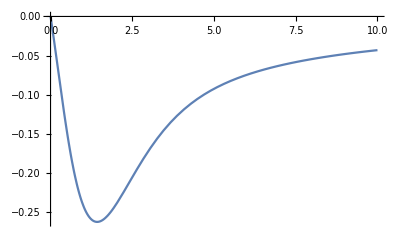

```mathematica
Plot[1/2 x^3 MeijerG[{{-1,-1/2},{}},{{-1,0},{-3/2,1/2}},x^2],{x,0,10}]
```

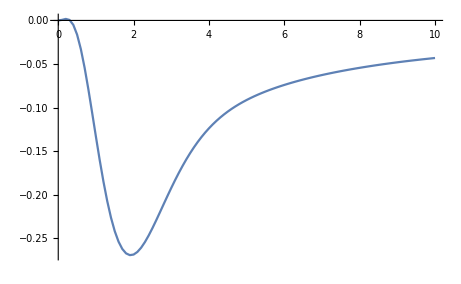

```mathematica
Block[{z=1+ⅈ},DiscretePlot[(1/2 z x^3 MeijerG[{{-1,-1/2},{}},{{-1,0},{-3/2,1/2}},z x^2]-1/2 Conjugate[z] x^3 MeijerG[{{-1,-1/2},{}},{{-1,0},{-3/2,1/2}},Conjugate[z] x^2])/(-ⅈ Im[z]),{x,0,10,1/10},Joined->True,Filling->None]]
```

```mathematica
Integrate[1/2 x^3 MeijerG[{{-1,-1/2},{}},{{-1,0},{-3/2,1/2}},a x^2],x]
```

1/4 x^4 MeijerG[{{-1,-1,-1/2},{}},{{-1,0},{-2,-3/2,1/2}},a x^2]

```mathematica
N[(1/4 z x^4 MeijerG[{{-1,-1,-1/2},{}},{{-1,0},{-2,-3/2,1/2}},z x^2]-1/4 Conjugate[z] x^4 MeijerG[{{-1,-1,-1/2},{}},{{-1,0},{-2,-3/2,1/2}},Conjugate[z] x^2])/(-ⅈ Im[z])/.{x->3,z->1+ⅈ}]
```

-0.498649+0. ⅈ

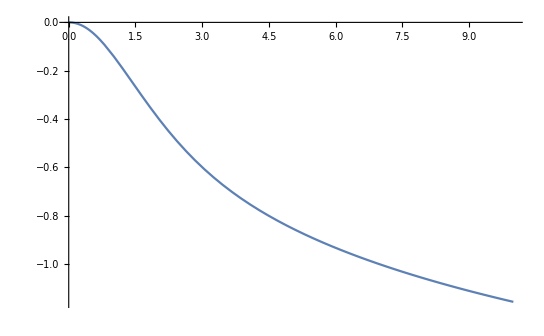

```mathematica
Plot[1/4 x^4 MeijerG[{{-1,-1,-1/2},{}},{{-1,0},{-2,-3/2,1/2}},x^2],{x,0,10}]
```

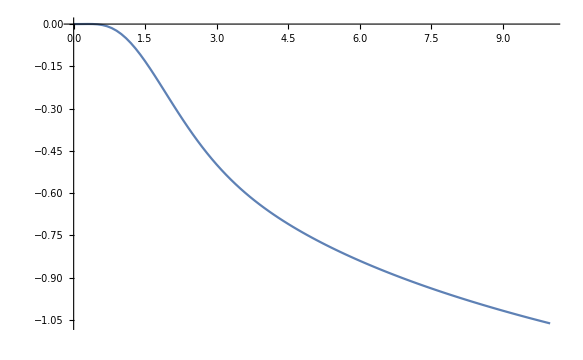

```mathematica
Block[{z=1+ⅈ},DiscretePlot[(1/4 z x^4 MeijerG[{{-1,-1,-1/2},{}},{{-1,0},{-2,-3/2,1/2}},z x^2]-1/4 Conjugate[z] x^4 MeijerG[{{-1,-1,-1/2},{}},{{-1,0},{-2,-3/2,1/2}},Conjugate[z] x^2])/(-ⅈ Im[z]),{x,0,10,1/10},Joined->True,Filling->None]]
```